## Log-Normal Evaluation

Derive values of f(x), g(x), K

```mathematica
Clear["p","k","μ","σ","x","τ","K","f","g"]
Remove["p","f","α","k"]
$Assumptions=σ>0&&σ∈Reals&&μ >0&&μ∈Reals&& x∈Reals && x>0;
p= PDF[LogNormalDistribution[Log[μ],σ],x]
f=k/2 FullSimplify[D[Log[p],x]]
α=Mean[TransformedDistribution[x f,x\[Distributed]LogNormalDistribution[Log[μ],σ]]]/Variance[TransformedDistribution[x ,x\[Distributed]LogNormalDistribution[Log[μ],σ]]]

K=k/.Solve[α==-1/τ,k][[1]]
f=f/.k-> K
```

Piecewise[{{(ⅇ^(-(Log[x]-Log[μ])^2/(2 σ^2)))/(√(2 π) x σ), x>0}, {0, True}}]

-(k (σ^2+Log[x]-Log[μ]))/(2 x σ^2)

-(ⅇ^(-σ^2) k)/(2 (-1+ⅇ^(σ^2)) μ^2)

(2 ⅇ^(σ^2) (-1+ⅇ^(σ^2)) μ^2)/τ

-(ⅇ^(σ^2) (-1+ⅇ^(σ^2)) μ^2 (σ^2+Log[x]-Log[μ]))/(x σ^2 τ)

```mathematica
ClearAll["f[t]","g[t]","x","y","f","g","μ","σ","τ"];
μ=1;
σ=.2;
τ=.2;
tSample = .01;
```

```mathematica
K=(2 ⅇ^(σ^2) (-1+ⅇ^(σ^2)) μ^2)/τ;
f[t]=-(σ^2+Log[y[t]]-Log[μ])/(y[t] σ^2);
g[t]=Sqrt[K];

proc=StratonovichProcess[ⅆy[t]==K/2 f[t]ⅆt+g[t]ⅆw[t],y[t],{y,μ},
t,w\[Distributed]WienerProcess[]]
sample = RandomFunction[proc,{0.,50,tSample}]
```

ItoProcess[{{0.-(5.30954 (0.04+Log[y[t]]))/y[t]},{{0.651738}},y[t]},{{y},{1}},{t,0}]

TemporalData[…]

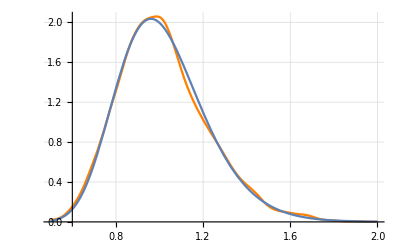

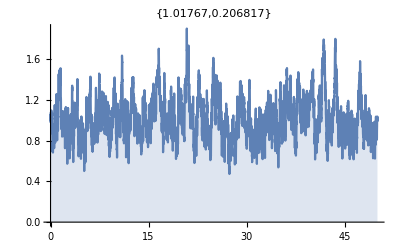

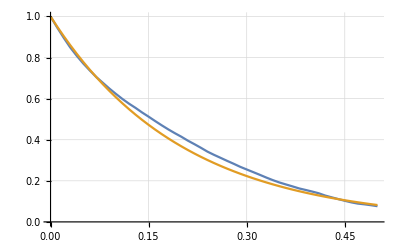

```mathematica
(*SmoothHistogram[sample,GridLines->Automatic]*)
Show[{Plot[PDF[SmoothKernelDistribution[sample],x],{x,.5,2},PlotStyle->Orange],Plot[PDF[LogNormalDistribution[Log[μ],σ],x],{x,.5,2}]},GridLines->Automatic]
ListLinePlot[sample,Filling->Axis,PlotLabel->{Mean[sample],StandardDeviation[sample]}]
ListLinePlot[
{Table[{x*tSample,CovarianceFunction[sample,x]/CovarianceFunction[sample,0]},{x,0,50}],
Table[{x*tSample,Exp[-x*tSample/τ]},{x,0,50}]},PlotRange->Full,GridLines->Automatic]
```